```mathematica
d=Daljica[{-1,1},{3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
Dolzina[Daljica[AA_,BB_]] := Norm[BB-AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line [{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_] := Graphics[Slika[d]]
```

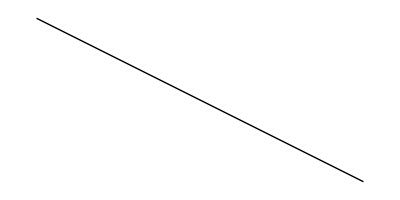

```mathematica
Narisi[d]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, n, k},
{x1, y1}= AA;
{x2, y2} = BB;
k= (y2-y1)/(x2-x1);
n= n/.First[Solve[y1== k*x1+n,n]];
y == k*x+n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
dd=Daljica[{-4,5},{55,-32}]
```

```mathematica
Daljica[{-4,5},{1,-3}]
```

Daljica[{-4,5},{1,-3}]

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{a, b},
a = EnacbaNosilke[d];
b = EnacbaNosilke[dd];
rešitev= Solve[a&&b, {x, y}]
]
```

```mathematica
Presek[d, dd]
```

{{x→47/3,y→-22/3}}

```mathematica
{-1,1}
```

{-1,1}

```mathematica
?d
```

Global`d

d=Daljica[{-1,1},{3,-1}]

```mathematica
?dd
```

Global`dd

dd=Daljica[{-1,1},{55,-32}]

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{
Graphics[
```